## Lagrange Interpolation

### Initialization:

```mathematica
g[x_] :=Cos[x];
points := { {-2,N[g[-2]]}, {0, N[g[0]]} , {1, N[g[1]]}, {3, N[g[3]]}}
Print[points]
```

{{-2,-0.416147},{0,1.},{1,0.540302},{3,-0.989992}}

### Where the magic happens ....

{{-2,-0.909297},{0,0.},{1,0.841471},{3,0.14112}}[1][2]

```mathematica
n=Length[points];
term:=1;
expression:=0;

Do[term:=1;
Do[
If[j!=i,
term*=(x-points[[j]][[1]])/(points[[i]][[1]]-points[[j]][[1]]),],
{j,1,n}];
expression+=term*points[[i]][[2]];,{i,1,n}];

p=Function[{x},Evaluate[expression]];
estimatedPoints=Table[{points[[i]][[1]],p[points[[i]][[1]]]},{i,1,n}];
estimatedPoints
```

{{-2,-0.416147},{0,1.},{1,0.540302},{3,-0.989992}}

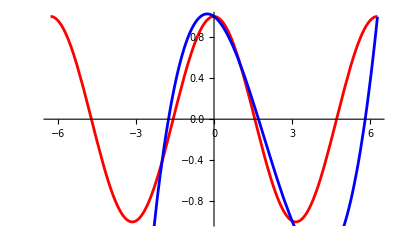

```mathematica
r:=Plot[g[x], {x, -2*Pi, 2*Pi},PlotStyle->Red];
h := Plot[p[x], {x,-2*Pi,2*Pi}, PlotStyle->Blue];
Show[r, h]
(*Plotting interpolated polynomial p(x) and main function g(x) *)
```